# driving w Jim’s board ultima ~50 Hz corner freq

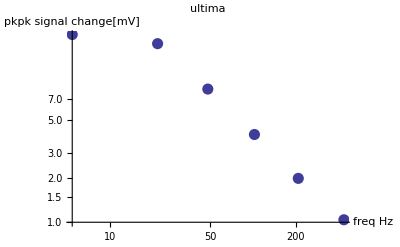

```mathematica
pkpk={19.4,8.2,16.8,4,2,1.04};
freq={5.445,48.34,21.53,102.4,207.5,432.6};
dat=Sort[Thread[{freq,pkpk}]];
ListLogLogPlot[dat,PlotStyle->PointSize[.02],AxesLabel->{"freq Hz","pkpk signal change[mV]"},PlotLabel->"ultima"]
```

# driving w Jim’s board suprema ~50 Hz corner freq

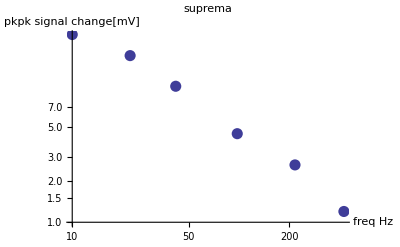

```mathematica
pkpk={24,16.8,10,4.48,2.64,1.2};
freq={10,22.24,41.74,97.6,216.6,425.5};
dat=Sort[Thread[{freq,pkpk}]];
ListLogLogPlot[dat,PlotStyle->PointSize[.02],AxesLabel->{"freq Hz","pkpk signal change[mV]"},PlotLabel->"suprema"]
```

# driving w tpz001

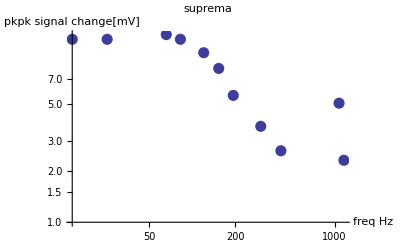

```mathematica
pkpk={8.08,12.8,12,12,12,10,5.6,3.68,2.64,2.32,5.04};
freq={153.4,65.67,25.23,14.34,82.5,120.3,194.1,302.8,419.3,1162,1075};
dat=Sort[Thread[{freq,pkpk}]];
ListLogLogPlot[dat,PlotStyle->PointSize[.02],AxesLabel->{"freq Hz","pkpk signal change[mV]"},PlotLabel->"suprema"]
```

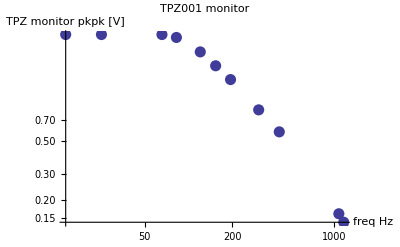

```mathematica
pkpk={1.64,2.68,2.68,2.68,2.56,2.04,1.32,.82,.58,.14,.16};
freq={153.4,65.67,25.23,14.34,82.5,120.3,194.1,302.8,419.3,1162,1075};
dat=Sort[Thread[{freq,pkpk}]];
ListLogLogPlot[dat,PlotStyle->PointSize[.02],AxesLabel->{"freq Hz","TPZ monitor pkpk [V]"},PlotLabel->"TPZ001 monitor"]
```

```mathematica
(D[Exp[-x^2/(2 σ^2)], x])/.x->σ
```

-1/(√ⅇ σ)

```mathematica
Exp[-1/2]/σ
```

1/(√ⅇ σ)

```mathematica
Ex
```

```mathematica
Solve[Exp[-x^2/(2 σ^2)]==1/Exp[2],x]
```

{{x→ConditionalExpression[-√2 σ √(2+2 ⅈ π C[1]),C[1]∈Integers]},{x→ConditionalExpression[√2 σ √(2+2 ⅈ π C[1]),C[1]∈Integers]}}

```mathematica
1.2/4
```

0.3

```mathematica
FullSimplify[(Integrate[A Exp[-x^2/(2 σ^2)],{x,-Infinity,σ+dx}]-Integrate[A Exp[-x^2/(2 σ^2)],{x,-Infinity,σ-dx}])/Integrate[A Exp[-x^2/(2 σ^2)],{x,-Infinity,σ}]]
```

ConditionalExpression[(√(1/σ^2) σ (-Erf[(-dx+σ)/(√2 σ)]+Erf[(dx+σ)/(√2 σ)]))/(1+√(1/σ^2) σ Erf[1/(√2)]),Re[1/σ^2]>0]

```mathematica
(Erf[(dx+σ)/(√2 σ)]-Erf[(-dx+σ)/(√2 σ)])/(1+Erf[1/(√2)])/.σ->0.3/.dx->.001
```

0.00191733

```mathematica
0.4/200
```

0.002

```mathematica
8 1.4
```

11.2

# .0044 pk-pk displacement at 8 in. per mVpp.